```mathematica
f[k_]:=1/(1.0+Exp[(k^2-Ef)/T])
```

```mathematica
Ef=3.68317
```

3.68317

```mathematica
T=2
```

2

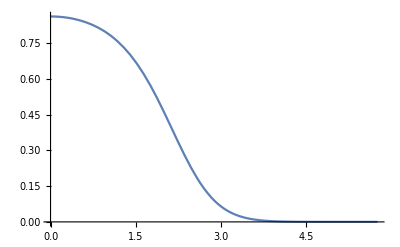

```mathematica
Plot[f[k], {k,0,3*Sqrt[Ef]}]
```

```mathematica
chi=2*1/T*NIntegrate[4*π*k^2*(f[k]^2-f[k]),{k,0, Infinity}]/(2.0*π)^3
```

-0.0887264

```mathematica
NIntegrate[4*π*k^2*(f[k]),{k,0, Infinity}]/(2.0*π)^3
```

0.720273

```mathematica
NIntegrate[4*π*k^2*(f[k]^2),{k,0, Infinity}]/(2.0*π)^3
```

0.186335

```mathematica
chi=2.0*NIntegrate[(f[Sqrt[(kx+3.8683)^2+ky^2+kz^2]]-f[Sqrt[kx^2+ky^2+kz^2]])/((kx+3.8683)^2-kx^2),{kx, -Infinity, Infinity},{ky, -Infinity,Infinity},{kz,-Infinity,Infinity}, PrecisionGoal->4]/(2.0*π)^3
```

-0.0542927